ⅇ^(-k^2/4) √π

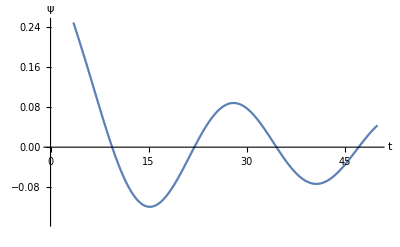

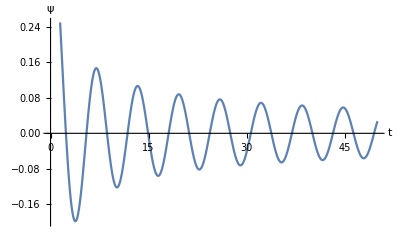

ConditionalExpression[(ⅇ^(t^2/(-1-4 ⅈ t)))/(√(1+4 ⅈ t)), Im[t]<1/4]

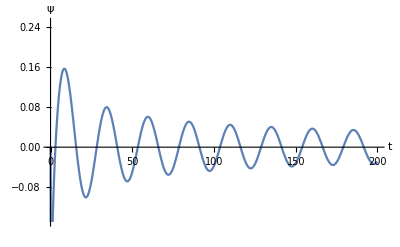

ConditionalExpression[(ⅇ^((4 t^2)/(-1-4 ⅈ t)))/(√(1+4 ⅈ t)), Im[t]<1/4]

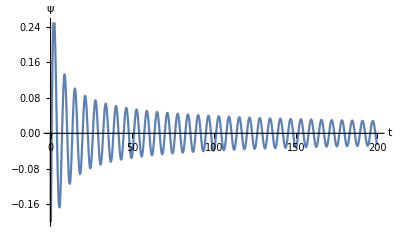

InverseFourier::nonopt: Options expected (instead of t) beyond position 2 in InverseFourier[ⅈ √(2 π) DiracDelta[-ⅈ i k+omega] Sign[omega],omega,t]. An option must be a rule or a list of rules.

```mathematica
a[k_] = Limit[Integrate[Exp[-ⅈ*k*x-x*x],{x,-R,R}],R->Infinity]

Plot[Exp[-1/16]*Cos[(t-π)/4]/(2*Sqrt[t]),{t,0,200}, PlotRange ->{-0.15,0.25},PlotPoints->1000, AxesLabel -> {t,ψ}]
Plot[Exp[-1/4]*Cos[t-π/4]/(2*Sqrt[t]),{t,0,200}, PlotRange ->{-0.2,0.25},PlotPoints->1000, AxesLabel -> {t,ψ}]

b1[t_]=Integrate[a[k]*Exp[ⅈ*k*(1-k)*t]/(2*π),{k,-Infinity,Infinity}]
Plot[Re[b1[t]],{t,0,200}, PlotRange ->{-0.15,0.25},PlotPoints->10000, AxesLabel -> {t,ψ}]

b2[t_]=Integrate[a[k]*Exp[ⅈ*k*(2-k)*t]/(2*π),{k,-Infinity,Infinity}]
Plot[Re[b2[t]],{t,0,200}, PlotRange ->{-0.2,0.25},PlotPoints->10000, AxesLabel -> {t,ψ}]
```